## Rotor potential - θ dependence

```mathematica
I1=20;
I2=100;
I3=40;
A1=1/(2I1);
A2=1/(2I2);
A3=1/(2I3);
j=6.5;
θ=π/6;
aFct[spin_,a1_,a2_,th_]:=a2-(1-(j*Sin[th])/spin)-a1;
uFct[spin_,a1_,a2_,a3_,th_]:=(a3-a1)/aFct[spin,a1,a2,th];
k[spin_,a1_,a2_,a3_,th_]:=√uFct[spin,a1,a2,a3,th];
q[spin_,a1_,a2_,a3_,th_]:=∫_0^ϕ (1-k[spin,a1,a2,a3,th]^2*Sin[t]^2)^(-1/2)ⅆt;
```

### generating a table with q values for different ϕ

```mathematica
(*qTable=Table[{fi,q[45/2,A1,A2,A3,θ]/.ϕ->fi},{fi,-π/2,π/2,π/16}];*)
```

```mathematica
jacobi[q_]:=Re[JacobiAmplitude[q,k[45/2,A1,A2,A3,θ]^2]];
```

### 4th order series expansion of the function k in terms of the coupling angle θ

```mathematica
(*FullSimplify[Series[k[i,a1,a2,a3,x],{x,0,4}]];*)
```

## the formula for the series expansion of k in variable θ up to 4th order

```mathematica
SeriesData[x, 0, {Sqrt[(a1 - a3)/(1 + a1 - a2)], (3.25*Sqrt[(a1 - a3)/(1 + a1 - a2)])/
    ((1. + a1 - 1.*a2)*i), (15.84375*Sqrt[(a1 - a3)/(1 + a1 - a2)])/
    ((1. + a1 - 1.*a2)^2*i^2), (Sqrt[(a1 - a3)/(1 + a1 - a2)]*
     (85.82031250000001 + (-0.5416666666666666*a1^2 - 0.5416666666666666*
         (1. - 1.*a2)^2 + a1*(-1.0833333333333333 + 1.0833333333333333*a2))*i^2))/
    ((1. + a1 - 1.*a2)^3*i^3), (Sqrt[(a1 - a3)/(1 + a1 - a2)]*
     (488.10302734375 + (-5.28125*a1^2 - 5.28125*(1. - 1.*a2)^2 + 
        a1*(-10.5625 + 10.5625*a2))*i^2))/((1. + a1 - 1.*a2)^4*i^4)}, 0, 5, 1];
```

## numerical application for k and k-expanded

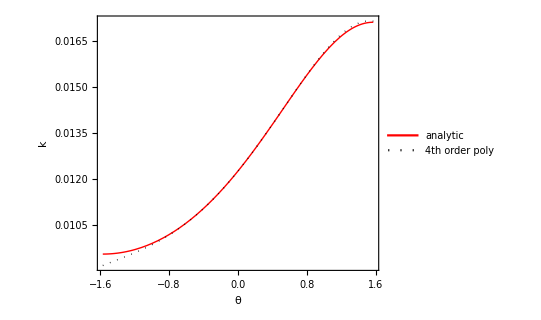

```mathematica
fk[x_]:=(√(5/102))/2+0.015676734084996244 x+0.003330025214133189 x^2-0.0018268353506996008 x^3-0.0009152323061940534 x^4;
Plot[{k[45/2,A1,A2,A3,x]^2,fk[x]^2},{x,-π/2,π/2},Frame->True,Axes->False,PlotStyle->{{Red,Thick},{Black,Dotted,Thick}},FrameStyle->Directive[Black,Thick],FrameLabel->{"θ","k"},AspectRatio->0.8,PlotLegends->Placed[{"analytic","4th order poly"},{0.25,0.75}],LabelStyle->{15,Bold,Black,FontFamily->"Times New Roman"}]
```

```mathematica
kValueInPlot=k[45/2,A1,A2,A3,θ];
```

## expansion of Jacobi’s s function

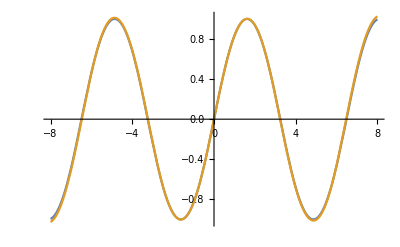

```mathematica
snSeriesFunc[z_,m_]:=Normal[Series[JacobiSN[z,m],{m,0,1}]];
Plot[{JacobiSN[x,kValueInPlot],snSeriesFunc[q,k]/.{q->x,k->kValueInPlot}},{x,-8,8}]
```

```mathematica
snSeriesFunc[x,k]/.{x->q,k->kValueInPlot}
```

Sin[q]+0.0149356 Cos[q] (-2 q+Sin[2 q])

## expansion of Jacobi’s c function

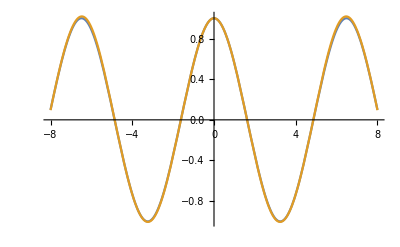

```mathematica
cnSeriesFunc[z_,m_]:=Normal[Series[JacobiCN[z,m],{m,0,1}]];
Plot[{JacobiCN[x,kValueInPlot],cnSeriesFunc[q,k]/.{q->x,k->kValueInPlot}},{x,-8,8}]
```

```mathematica
cnSeriesFunc[x,k]/.{x->q,k->kValueInPlot}
```

Cos[q]-0.0149356 Sin[q] (-2 q+Sin[2 q])

## expansion of Jacobi’s d function

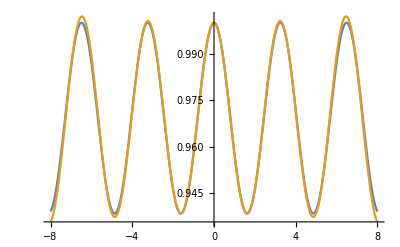

```mathematica
dnSeriesFunc[z_,m_]:=Normal[Series[JacobiDN[z,m],{m,0,2}]];
dnSeries[z_,m_]:=1-1/2 Sin[z]^2 m-1/32 (Sin[z] (-8 z Cos[z]+5 Sin[z]+Sin[3 z])) m^2;
Plot[{JacobiDN[x,kValueInPlot],dnSeriesFunc[q,k]/.{q->x,k->kValueInPlot}},{x,-8,8}]
```

## solve the q coordinate for the expanded k to 4th order in θ

```mathematica
fivalue=N[π/2];
```

```mathematica
qPoly[arg_]:=∫_0^fivalue (1-fk[arg]^2 Sin[t]^2)^(-1/2)ⅆt;
qPolyTable=Table[{i,qPoly[i*π/180]},{i,-180,180,1}];
```

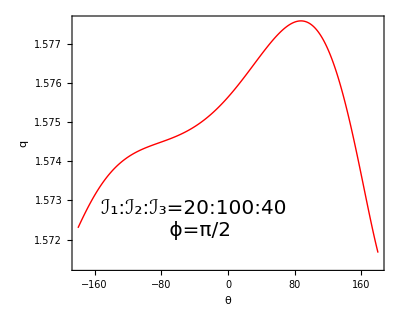

```mathematica
ListPlot[qPolyTable,Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ","q"},PlotStyle->{Red,Thick},AspectRatio->0.8,LabelStyle->{Bold,Black,16,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:`` \n ϕ=π/2"][I1,I2,I3],20,FontFamily->"Times New Roman"],Scaled[{0.4,0.2}]]]
```

## solve the q coordinate for analytical expression of k

```mathematica
kfct[th_]:=k[45/2,A1,A2,A3,th];
```

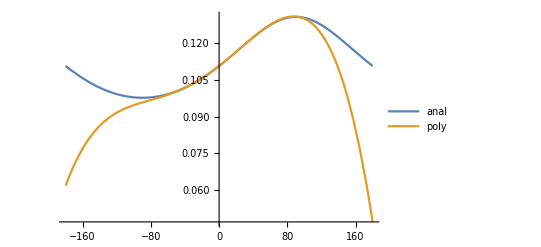

```mathematica
Plot[{kfct[x*π/180],fk[x*π/180]},{x,-180,180},PlotLegends->{"anal","poly"}]
```

```mathematica
qAnal[arg_]:=∫_0^fivalue (1-kfct[arg]^2 Sin[t]^2)^(-1/2)ⅆt;
qAnalTable=Table[{i,qAnal[i*π/180]},{i,-180,180,1}];
```

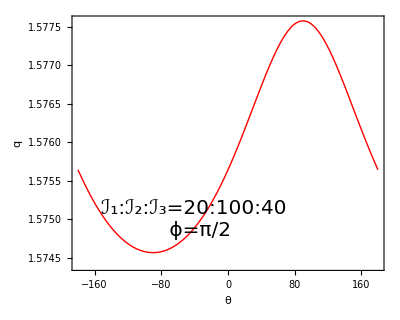

```mathematica
ListPlot[qAnalTable,Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ","q"},PlotStyle->{Red,Thick},AspectRatio->0.8,LabelStyle->{Bold,Black,16,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:`` \n ϕ=π/2"][I1,I2,I3],20,FontFamily->"Times New Roman"],Scaled[{0.4,0.2}]]]
```

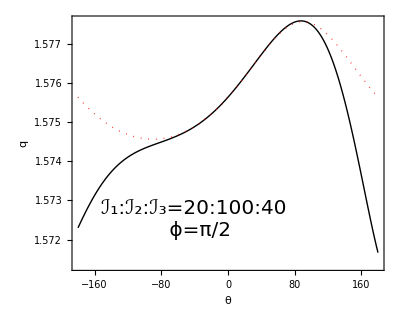

```mathematica
ListPlot[{qPolyTable,qAnalTable},Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ","q"},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},AspectRatio->0.8,LabelStyle->{Bold,Black,16,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:`` \n ϕ=π/2"][I1,I2,I3],20,FontFamily->"Times New Roman"],Scaled[{0.4,0.2}]]]
```

## Working with the JacobiAmplitude as function of θ

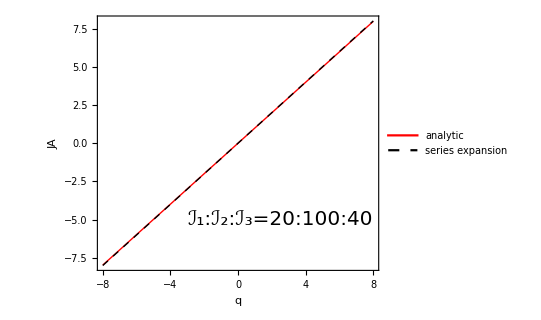

```mathematica
jaAnal[q_,th_]:=JacobiAmplitude[q,kfct[th]^2];
jaAnalTable=Table[{x,jaAnal[x,θ]},{x,-8,8,1}];
jaPoly[q_,th_]:=Normal[Series[JacobiAmplitude[z,m],{z,0,2}]]/.{z->q,m->kfct[th]^2};
jaPolyTable=Table[{x,jaPoly[x,θ]},{x,-8,8,1}];ListPlot[{jaAnalTable,jaPolyTable},Joined->True,PlotLegends->Placed[{"analytic","series expansion"},{0.3,0.75}],PlotStyle->{{Red,Thick},{Black,Thick,Dashed}},Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"q","JA"},PlotStyle->{{Black,Thick},{Red,Thick,Dotted}},AspectRatio->0.8,LabelStyle->{Bold,Black,16,FontFamily->"Times New Roman"},Epilog->Inset[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:``"][I1,I2,I3],20,FontFamily->"Times New Roman"],Scaled[{0.65,0.2}]]]
```